# Wolfram语言专题讲座 机器学习和人工智能

杨圣汇 Wolfram Research Inc

## 提纲

### 机器学习总览

什么是机器学习

Wolfram语言的内置机器学习函数和功能

Wolfram 神经网络在线库

一小时AI入门系列

### 监督学习

监督学习 VS 非监督学习

什么类型的问题最适合用分类法求解？

分类：一种监督学习的任务

Classify 函数介绍

定制 Classify 函数

## 什么是机器学习

插值拟合

```mathematica
data=;
```

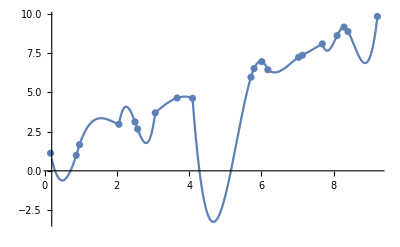

```mathematica
Show[Plot[f[x],{x,0.2,9.2},PlotRange->All],lp]
```

回归

```mathematica
nbasis[n_Integer][x_]:=Table[x^k,{k,0,n}]
Manipulate[
fit=Fit[data,nbasis[n][x],x];
Show[Plot[fit,{x,0,15},PlotRange->All],lp,PlotRange->{{0,10},{0,15}},PlotLabel->"n = "<>ToString[n]],
{n,1,20,2},SaveDefinitions->True]
```

让计算机根据给定的示例自动学习，并接下来判断需要做什么

监督学习: 示例已经被标记完成

无监督学习: 示例没有被打上标记

## Wolfram语言的内置机器学习函数和功能

图片内容的自动识别

```mathematica
ImageIdentify[ {-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{space station,earth,ballistic capsule,sun}

```mathematica
Entity["Star","Sun"]
```

网页版图片识别器/发布日博客

语言类型识别

```mathematica
LanguageIdentify[{"hallo en welkom","नमस्ते और आपका स्वागत हैै","أهلا ومرحبا", "নমস্কার এবং স্বাগত","హలో మరియు స్వాగతం","你好，歡迎光臨","Bonjour et bienvenue","こんにちは、いらっしゃい","ಹಲೋ ಮತ್ತು ಸ್ವಾಗತ","hujambo na karibu","привіт і ласкаво просимо","ہیلو اور خوش آمدید"}]
```

{Dutch,Hindi,Arabic,Bengali,Telugu,Chinese,French,Japanese,Kannada,Swahili,Ukrainian,Urdu}

名人肖像识别

```mathematica
Classify["NotablePerson", {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{Nelson Mandela,Mahatma Gandhi,Albert Einstein,Mother Teresa,Rosa Parks,Marie Curie}

返回结果是 Entity 类型；各类分类器和神经网络模块保存位置

```mathematica
$UserBasePacletsDirectory//SystemOpen
```

石头剪刀布

```mathematica
sp = SequencePredict[{{-Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-}}]
```

SequencePredictorFunction[…]

```mathematica
sp[{-Graphics-, -Graphics-}]
```

-Graphics-

```mathematica
sp[{-Graphics-, -Graphics-},"Probabilities"]
```

<|-Graphics-→0.370295,-Graphics-→0.422177,-Graphics-→0.207528|>

根据特征空间进行分组

```mathematica
FeatureSpacePlot[{-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}]//Framed
```

-Graphics-

## 内置机器学习函数: 通过名称调用的分类器

分析文本中的情感

正向情感

```mathematica
Classify["Sentiment","I'm so excited to be programming"]
```

Positive

消极情感

```mathematica
Classify["Sentiment","math can be really hard"]
```

Negative

指明文本中的主题

```mathematica
Classify["FacebookTopic", "I love eating carrots in the morning"]
```

FoodAndDrink

```mathematica
Classify["FacebookTopic", "Happy Birthday"]
```

SpecialOccasions

## 监督学习 VS 无监督学习

### 无标记数据集

```mathematica
FindClusters[{-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

### 有标记数据集

```mathematica
c = Classify[<|"cat"-> {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-},"car"-> { -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}|>]
```

ClassifierFunction[…]

```mathematica
c[{-Graphics-,-Graphics-}]
```

{car,cat}

## 通过机器学习分类能够回答的问题有哪些？

是 A 或 B? （两个类别）

样本属于第一类或者第二类？

身体组织的图片样本是健康组织还是癌症组织？

这份贷款申请对于银行来讲是高风险的还是低风险的？

是 A, B, C 或者 D (多个类别)

图片中的动物是什么（老虎，狮子，猫，狗等多个类别）

自动驾驶系统判断出路上的物体是什么？

## 分类: 一种监督学习的任务

内置机器学习超级函数 Classify 进行性分类

### 基本示例

```mathematica
trainingset={1->"A",2->"A",3.5->"B",4->"B"};
```

```mathematica
c=Classify[trainingset]
```

ClassifierFunction[…]

```mathematica
c[1.2]
```

A

```mathematica
daynight=Classify[
{-Graphics-->"Night",-Graphics-->"Day",-Graphics-->"Night",-Graphics-->"Night",-Graphics-->"Day",-Graphics-->"Night",-Graphics-->"Day",-Graphics-->"Day",-Graphics-->"Night",-Graphics-->"Night",-Graphics-->"Day",-Graphics-->"Night",-Graphics-->"Night",-Graphics-->"Day",-Graphics-->"Night",-Graphics-->"Night",-Graphics-->"Day",-Graphics-->"Day",-Graphics-->"Day",-Graphics-->"Day",-Graphics-->"Night",-Graphics-->"Night",-Graphics-->"Day",-Graphics-->"Night",-Graphics-->"Night",-Graphics-->"Day",-Graphics-->"Day",-Graphics-->"Day",-Graphics-->"Night",-Graphics-->"Day"}]
```

ClassifierFunction[…]

在新数据上面测试

```mathematica
daynight[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{Day,Day,Day,Night,Night,Night}

### 猫-狗分类器

训练样本

```mathematica
dogCatClassifier =Classify[ <|"cat"-> {-Graphics-,-Graphics-,-Graphics-},
"dog"-> {-Graphics-,-Graphics-,-Graphics-}|>]
```

ClassifierFunction[…]

在新样本上面使用分类器

```mathematica
dogCatClassifier[-Graphics-]
```

dog

在不同数据样本上训练另一个分类器

```mathematica
dogCatClassifier2=Classify[{"the cat is grey"->-Graphics-,"my cat is fast"->-Graphics-,"this dog is scary"->-Graphics- ,"the big dog"->-Graphics-}]
```

ClassifierFunction[…]

在新数据上面测试分类器

```mathematica
dogCatClassifier2[{"nice cat","what a dog"}]
```

{-Graphics-,-Graphics-}

Classify 能够返回对于最有可能的分类判定或者相应的概率值

```mathematica
c=Classify[{
{1.5,Blue}->"A",
{3.2,Blue}->"A",
{4.1,Red}->"B",
{5.3,Red}->"B",
{10.,Green}->"C",
{12.4,Red}->"C"}]
```

ClassifierFunction[…]

判定

```mathematica
c[{10.1,Blue}]
```

C

最有可能的分类的概率值

```mathematica
c[{10.1,Blue},"TopProbabilities"]
```

{C→0.767341,A→0.232659}

```mathematica
c[{10.1,Blue},"Probabilities"]
```

<|A→0.232659,B→7.08733×10^-11,C→0.767341|>

```mathematica
c[{10.1,Blue},"Probability"-> "A"]
```

0.232659

特征 VS 分类概率的函数

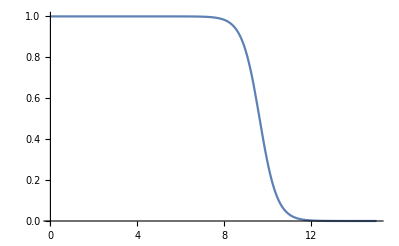

```mathematica
Plot[c[{x,Blue},"Probability"->"A"],{x,0,15},Exclusions->None]
```

## 分类器评估

ClassifierMeasurements 分析 Classify 返回的结果
案例使用经典的 Fisher's Iris 数据集

```mathematica
irisData = ExampleData[{"MachineLearning","FisherIris"},"TrainingData"];
irisDataTest = ExampleData[{"MachineLearning","FisherIris"},"TestData"];
```

其中训练集大小

```mathematica
Length[irisData]
```

105

测试集大小

```mathematica
Length[irisDataTest]
```

45

训练模型

```mathematica
c=Classify[irisData]
```

ClassifierFunction[…]

预测 Iris 种类

```mathematica
c[{4.3,3.1,1.2,.3}]
```

setosa

在测试数据集上评估模型

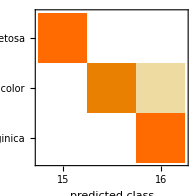
Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 45
Accuracy | (97.82.2) %
Accuracy baseline | (33.7.) %
Geometric mean of probabilities | 0.948 ± 0.037
Mean cross entropy | 0.0538 ± 0.039
Single evaluation time | 1.54 ms/example
Batch evaluation speed | 14.3 examples/ms
-Graphics- |

```mathematica
cm=ClassifierMeasurements[c,irisDataTest]
```

```mathematica
cm["Accuracy"]
```

0.977778

相当于

```mathematica
(15+14+15)/45.
```

0.977778

```mathematica
cm["ConfusionMatrixPlot"]
```

-Graphics-

ClassifierMeasurements 还可以使用以下属性

“ROCCurve”

“AreaUnderROCCurve”即 AUC

“FalsePositiveRate”

“Precision”

“Recall”

## 定制 Classify 函数功能和属性

随机设定一组训练集数据

```mathematica
trainingset = {1,2,3,4,5,6,7}-> {"a","a", "b", "a", "b","b","b"};
```

### Method

Classify 支持以下 Method 选项:

Decision tree/ 判别树

Gradient boosted trees/ 梯度增强

Logistic regression/ 逻辑回归

Nearest neighbors/ 邻近法

Naive Bayes/ 贝叶斯方法

Markov model/ 马克洛夫模型

Support vector machines/ 支持向量机

Random forests/ 随机森林

Neural networks/ 神经网络

### 使用逻辑回归

```mathematica
logistic=Classify[trainingset, Method->"LogisticRegression"]
```

ClassifierFunction[…]

### 朴素贝叶斯方法

```mathematica
naiveb=Classify[trainingset, Method->"NaiveBayes"]
```

ClassifierFunction[…]

通过测试集来比较分类器结果

```mathematica
testData = Table[i,{i,0,9,0.2}];
```

```mathematica
Short[testData]
```

{0.,0.2,0.4,0.6,0.8,1.,«34»,8.,8.2,8.4,8.6,8.8,9.}

```mathematica
logistic /@ testData
```

{a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b}

```mathematica
naiveb/@ testData
```

{a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b,b}

当特征从 0 到 8 变化时，两个分类器中判别为 “a”类型的概率也随之变化

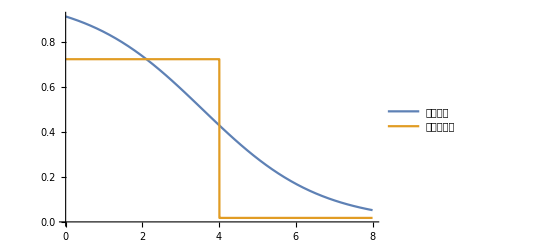

```mathematica
Plot[{
logistic[x,"Probability"->"a"],
naiveb[x,"Probability"->"a"]
}, {x,0,8}, Exclusions->None,PlotLegends->{"逻辑回归","朴素贝叶斯"}]
```

### PerformanceGoal 选项

分类器性能可以指定以下任意一种参数进行优化

Speed/训练速度

TrainingSpeed/实际训练用时

Quality/质量或者准度

Memory/内存占用

DirectTrainig/全数据训练

从训练集当中随机抽取样本

```mathematica
RandomSample[irisData,5]
```

优化训练时间

```mathematica
c1 = Classify[irisData,PerformanceGoal->"TrainingSpeed"]
```

ClassifierFunction[…]

优化训练精准度

```mathematica
c2 = Classify[irisData,PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

比较实际训练用时

```mathematica
Information[#, "TrainingTime"]&/@ {c1,c2}
```

{0.654894 s,2.11049 s}

## 学习资源

Elementary Introduction to the Wolfram Language: Chapter 22 | Machine Learning

Wolfram U 视频课程: Learning from Input and Output | Supervised Learning

Wolfram U 视频课程: An Overview of Machine Learning in the Wolfram Language

Wolfram语言最新特性: High-Level Machine Learning

Wolfram语言帮助文档: Machine Learning

## 衍生阅读

Boosting

XGBoost VS LightGBM